```mathematica
ClearAll["Global`*"]
```

```mathematica
lo[n_, k_ ]:= Sum[ (-1)^(j+1) lo[ Floor[n/j],k-1],{j,1,n}];lo[n_, 1] := Sum[ (-1)^(j+1) Log[j],{j,1,n}]
t[n_, a_] := Mod[n,a]-Mod[n-1,a]
lp[n_, k_,b_ ]:= Sum[ t[j,b] lp[ Floor[n/j],k-1,b],{j,1,n}];lp[n_, 1,b_] := Sum[ t[j,b] Log[j],{j,1,n}]
fa[n_,k_] := Sum[ 2^j Binomial[k,j] (-1)^j l1[n/2^j,k],{j,0,k}]+Sum[ 2^j Binomial[k-1,j-1](-1)^j Log[2] d1[n/2^j,k],{j,1,k}]

L1[n_, k_ ]:= Sum[ L1[Floor[n/j],k-1],{j,1,n}];L1[n_, 1] := Sum[ Log[j],{j,1,n}];L1[n_,0]:=1
L2[n_, k_ ]:= Sum[ L2[Floor[n/j],k-1],{j,2,n}];L2[n_, 1] := Sum[ Log[j],{j,2,n}]
D1[n_, k_] := Sum[ D1[Floor[n/j],k-1],{j,1,n}];D1[n_, 0] := 1
L2toL1[n_,z_]:=Sum[FactorialPower[z-1,a]/a! L2[n,a+1],{a,0,Log[2,n]}]
L2toL1x[n_,z_]:=Sum[Binomial[z-1,a] L2[n,a+1],{a,0,Log[2,n]}]
L1toL2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k-1,j-1] L1[n,j],{j,1,k}]

EL[n_, k_,b_ ]:= EL[n,k,b]=Sum[ EL[ n/j,k-1,b],{j,1,n}]-b Sum[ EL[ n/(j b),k-1,b],{j,1,n}];EL[n_, 1,b_] := EL[n,1,b]=Sum[ Log[j],{j,1,n}]-b Sum[ Log[j b],{j,1,n/b}]
LtoEL[n_,k_,b_] := Sum[ b^j Binomial[k,j] (-1)^j L1[n/b^j,k],{j,0,k}]+Sum[ b^j Binomial[k-1,j-1](-1)^j Log[b] D1[n/b^j,k],{j,1,k}]

EL1toL1[n_, b_] := Sum[ b^j EL[n/b^j,1,b],{j,0,Log[b,n]}] + Log[b]Sum[ b^j D1[n/b^j,1],{j,1,Log[b,n]}]

EL2[n_, k_,b_ ]:= EL2[n,k,b]=Sum[ EL2[ n/j,k-1,b],{j,2,n}]+b Sum[ EL2[ n/(j b),k-1,b],{j,1,n}];EL2[n_, 1,b_] := EL2[n,1,b]=Sum[ Log[j],{j,2,n}]+b Sum[ Log[j b],{j,1,n/b}]
EL2toEL1[n_,z_,b_]:=Sum[FactorialPower[z-1,a]/a! EL2[n,a+1,b],{a,0,Log[If[ b<2,b,2],n]}]
EL1toEL2[n_,k_,b_]:=Sum[(-1)^(k-j) Binomial[k-1,j-1] EL[n,j,b],{j,1,k}]
```

```mathematica
N[L2toL1x[100,0]]
```

94.0453

```mathematica
N[EL2toEL1[100,0,101]]
```

94.0453

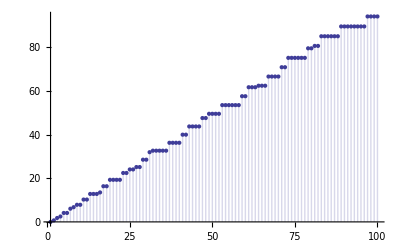

```mathematica
DiscretePlot[L2toL1[n,0],{n,1,100}]
```

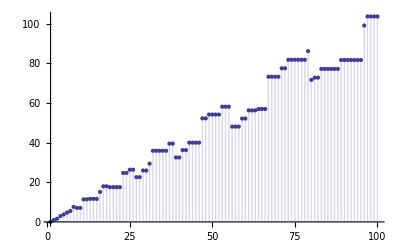

```mathematica
DiscretePlot[EL2toEL1[n,0,1.2],{n,1,100}]
```

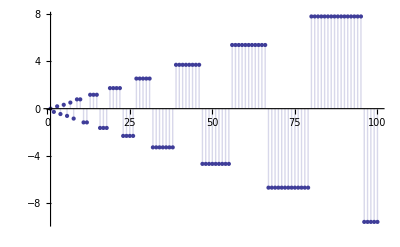

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,1.2],{n,1,100}]
```

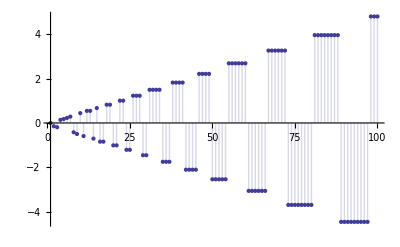

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,1.1],{n,1,100}]
```

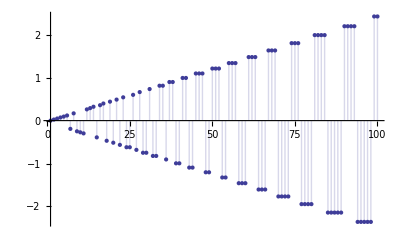

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,1.05],{n,1,100}]
```

```mathematica
N[Log[2 Pi]]
```

1.83788

```mathematica
fdif[n_,b_] := Sum[ (-1)^j Log[b^(b^j)],{j,1,Log[b,n]}]
```

```mathematica
N[fdif[100,1.00001]]
```

-0.000504998